```mathematica
list1 = Import[NotebookDirectory[]<>"/res/out_0.0_2.0.txt","Table"];
list2 = Import[NotebookDirectory[]<>"/res/out_0.1_2.0.txt","Table"];
Length[list1]
len=Length[list2[[1]]]
```

50

501

```mathematica
maxlist1=Map[Max,-list1]/Max[-list1[[1]]];
maxlist2=Map[Max,-list2]/Max[-list2[[1]]];
```

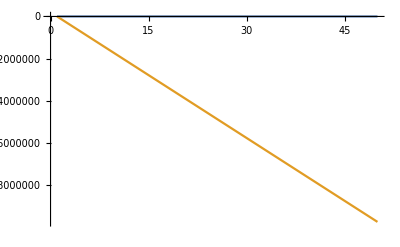

```mathematica
ListLinePlot[{maxlist1,maxlist2}]
```

```mathematica
enlist1=Map[Total[#^2]&,-list1];
enlist1=enlist1/Max[enlist1];
enlist2=Map[Total[#^2]&,-list2];
enlist2=enlist2/Max[enlist2];
```

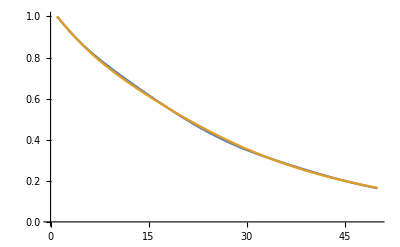

```mathematica
ListLinePlot[{enlist1,enlist2}]
```

```mathematica
list1 = Import[NotebookDirectory[]<>"/res/out_0.0_0.5.txt","Table"];
list2 = Import[NotebookDirectory[]<>"/res/out_5.8_0.5.txt","Table"];
```

```mathematica
max=Max[Max[Map[Max,-list1]],Max[Map[Max,-list2]]];
min=Min[Min[Map[Min,-list1]],Min[Map[Min,-list2]]];
Manipulate[
l1=-list1[[n]] + list1[[n,1]];
l2=-list2[[n]] + list2[[n,1]];
ListLinePlot[{l1,l2},PlotRange->Full],
{n,1,Length[list2],1}]
```